# 6.1 插值

## 1. 插值多项式

给定 n + 1 个插值点 (xi, f (xi))，i = 0, 1, …, n。构造次数至多 n 次的多项P (x), 使得P (xi) = f (xi).称P (x) 为f (x) 的插值多项式。
在实际应用中，这些插值点可能来自某次实验测量所得的数据，也可能来自某个复杂函数 的值。通过计算插值多项式，我们可以找到这些实验数据间的规律，或者使用简单的多项式函数 来近似复杂的函数。在数值计算方法中常用拉格朗日法牛顿法或样条函数构造插值多项式.

定理：给定n + 1 个点 (xi, f (xi))，i = 0, 1, …, n, 若 xi, xj 两两不同，则存在唯一一个次数不超过n的多项式Pn (x)，使得P (xi) = f (xi) 成立。

InterpolatingPolynomial[data, var]

#### 数据的输入方式如下：

InterpolatingPolynomial[{f1, f2, …}, x]，(1, f1), (2, f2), …确定的插值多项式

InterpolatingPolynomial[{{x_ 1, f_ 1}, {x_ 2, f_ 2}, …}, x],  (x_ 1, f_ 1), (x_ 2, f_ 2), …确定的插值多项式

InterpolatingPolynomial[{{{x_ 1, y_ 1, …}, f_ 1}, {{x_ 2, y_ 2, …}, f_ 2}, …}, {x, y, …}]
(x_ 1, y_ 1, …, f_ 1),  (x_ 2, y_ 2, …, f_ 2) …确定的插值多项式

InterpolatingPolynomial[{{{x_ 1, …}, f_ 1, df_ 1, …}, {{x_ 2, …}, f_ 2, df_ 2, …}, …}, {x, …}]
点 (x_ 1, ..., f_ 1) 及该点导数值，(x_ 2,  ..., f_ 2) 及该点导数值…确定的插值多项式

例题：根据下表构造插值多项式，并求6.12处近似值.
xi  | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
yi | 6.35 | 6.47 | 8.2 | 9.3 | 9.68 | 9.72 | 10.0 | 9.95

```mathematica
data1={6.35,6.47,8.2,9.3,9.68,9.72,10.0,9.95};
```

```mathematica
Clear[f]
```

```mathematica
f[x_]=InterpolatingPolynomial[data1,x]
```

9.95+(0.514286+(-0.117262+(0.0187024+(0.0275476+(-0.00770238+(0.00047619-0.000494048 (-3+x)) (-7+x)) (-2+x)) (-6+x)) (-4+x)) (-1+x)) (-8+x)

```mathematica
Expand[f[x]]
```

17.81-24.6275 x+18.9986 x^2-7.24275 x^3+1.61062 x^4-0.214208 x^5+0.0157917 x^6-0.000494048 x^7

```mathematica
f[6.12]
```

9.73101

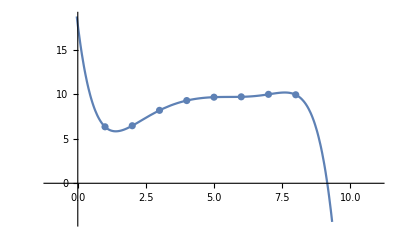

```mathematica
Show[Plot[f[x],{x,-1,11}],ListPlot[data1]]
```

例题：根据下表构造插值多项式 z = f (x, y)
x | 66 | 66 | 87 | 87 | 105 | 105 | 158 | 158
y | 9.8 | 10.3 | 9.7 | 13.5 | 9.9 | 14.2 | 9.6 | 12.5
z | 1.1 | 0.9 | 1.2 | 0.8 | 1.5 | 0.95 | 1.4 | 0.9

```mathematica
data2={{{66,9.8},1.1},{{66,10.3},0.9},{{87,9.7},1.2},{{87,13.5},0.8},{{105,9.9},1.5},{{105,14.2},0.95},{{158,9.6},1.4},{{158,12.5},0.9}};
```

```mathematica
g[x_,y_]=InterpolatingPolynomial[data2,{x,y}]
Expand[g[x,y]]
```

8.00127+x (0.436744+x (0.00100071-0.0000155277 x+0.000393981 y)-0.0926054 y)+(-2.31685+0.314061 y) y

8.00127+0.436744 x+0.00100071 x^2-0.0000155277 x^3-2.31685 y-0.0926054 x y+0.000393981 x^2 y+0.314061 y^2

```mathematica
point={{66,9.8,1.1},{66,10.3,0.9},{87,9.7,1.2},{87,13.5,0.8},{105,9.9,1.5},{105,14.2,0.95},{158,9.6,1.4},{158,12.5,0.9}};
```

```mathematica
Show[Plot3D[g[x,y],{x,66,160},{y,9.6,14.5}],ListPointPlot3D[point]]
```

-Graphics3D-

例题 : 按下列给定数据构造插值多项式：(0, f (0), f' (0)) = {0，-3.3, -2.2}, (1, f (1), f' (1)) = {1, -4.5, 0.8}.

```mathematica
data={{{0},-3.3,-2.2},{{1},-4.5,0.8}};
```

```mathematica
h[x_]=InterpolatingPolynomial[data,x]
```

-4.5+(-1+x) (0.8+(-1+x) (2.+1. x))

```mathematica
{h[0],h'[0],h[1],h'[1]}
```

{-3.3,-2.2,-4.5,0.8}

当数据点较多时，用InterpolatingPolynomial得到整区间的近似多项式， 其总体效
果就不一定好， 而且还常引起区间[x_0 ,x_n]端点处附近的剧烈振荡， 从而
产生出很大的误差.

```mathematica
tab=Table[{x,Sin[x]},{x,0,Pi,0.02}];
sin=InterpolatingPolynomial[tab,x];
```

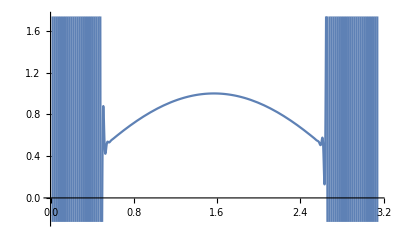

```mathematica
Plot[sin,{x,0,Pi}]
```

InterpolatingPolynomia[]，可以将插值函数表达式显示出来.但多数情况下，构造插值函数目的侧重计算一些函数值，并不在意插值函数的具体表达式，

### 2. 分段区间上的插值函数

Interpolation[{f1, f2, …}] 对应 x 值 1、2、…，构造函数值 fi 的插值.

Interpolation[{{x1, f1}, {x2, f2}, …}] 对应 x 的值 xi，构造函数值 fi 的插值.

Interpolation[{{{x1, y1, …}, f1}, {{x2, y2, …}, f2}, …}] 构造多维数据的插值.

Interpolation[{{{x1, …}, f1, df1, …}, …}] 构造一个插值，再现导数及函数值.

Interpolation[data, x] 在点 x 求 data 的插值

函数说明：Interpolation 返回一个 InterpolatingFunction 对象.
Interpolation[data] 返回的插值函数与每个点处的 data 一致.

Interpolation 的算法是在连续数据点间拟合多项式曲线.
多项式曲线的次数由选项 InterpolationOrder 指定.默认设置是 InterpolationOrder -> 3. 
可以通过使用设置 InterpolationOrder -> 1 进行线性插值.

Interpolation 支持 Method 选项.可能的设置包括表示样条插值的 "Spline" 和厄米特插值的 "Hermite".

Interpolation[data, InterpolationOrder -> n, Method ->" Spline"]

例题：已知原始数据x = (l, 2, 4, 5)，y = (16, 12, 8, 9)，试求子区间上的低次插值多项式Pr (x) 在插值点x = 1.2 处的值, r 依次取 1，2, 3.

```mathematica
data1={{1,16},{2,12},{4,8},{5,9}};
p1=Interpolation[data1,InterpolationOrder->1]
p2=Interpolation[data1,InterpolationOrder->2]
p3=Interpolation[data1,InterpolationOrder->3]
{p1[1.2],p2[1.2],p3[1.2]}
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

{15.2,15.0933,15.1307}

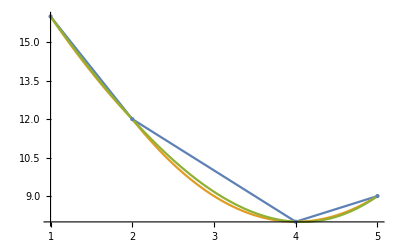

```mathematica
Show[Plot[{p1[x],p2[x],p3[x]},{x,1,5}],ListPlot[data1,PlotStyle->PointSize[Large]]]
```

给定 4 个插值点，构造的插值多项式函数的次数至多为 3 次

```mathematica
Interpolation[data1,InterpolationOrder->4]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {3}.

例题 : 取 f (x) = x^5 - 3 x^2 + 1 的函数值和一阶导数值构造三次样条插值，用插值函数计算
 x = 0.27 的函数值，并观察插值误差.

```mathematica
f[x_]=x^5-3x^2+1;
tt=Table[Evaluate[{{x},f[x],D[f[x],x]}],{x,0,2,0.3}];
```

```mathematica
p=Interpolation[tt]
```

InterpolatingFunction[…]

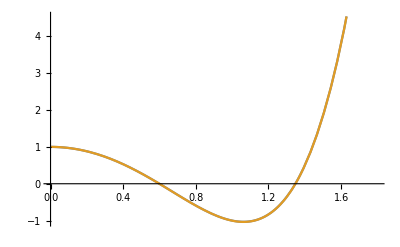

```mathematica
Plot[{f[x],p[x]},{x,0.,1.7999999999999998}]
```

```mathematica
{p[0.27],f[0.27]}
```

{0.782678,0.782735}

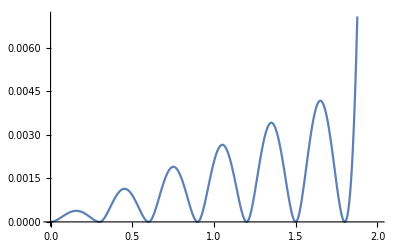

```mathematica
Plot[f[x]-p[x],{x,0,2}]
```

例题：对随机数据，比较样条插值和分段厄米特插值

```mathematica
data=Transpose[{Range[0,10]/10,RandomReal[1,11]}]
```

{{0,0.88952},{1/10,0.547648},{1/5,0.306479},{3/10,0.494605},{2/5,0.267906},{1/2,0.367275},{3/5,0.317856},{7/10,0.310435},{4/5,0.00111996},{9/10,0.795638},{1,0.341068}}

```mathematica
q1=Interpolation[data,Method->"Spline"]
q2=Interpolation[data,Method->"Hermite"]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

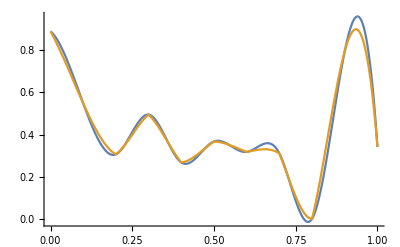
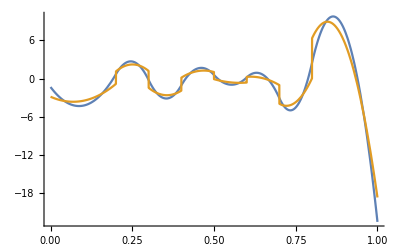

```mathematica
Row[{Plot[{q1[x],q2[x]},{x,0,1},PlotRange->All],Plot[{q1'[x],q2'[x]},{x,0,1},PlotRange->All]}]
```

3. 构造逼近函数
在计算一些复杂函数时，用函数Functionlnterpolation 可对复杂函数构造相对简单的 逼近函数简化计算。Functionlnterpolation生成插值形式函数。

FunctionInterpolation[expr, {x, xmin, xmax}]
对 x 从 xmin 到 xmax 计算 expr，并且构造一个 InterpolatingFunction 对象，这个对象表示对应于结果的近似函数.

FunctionInterpolation[expr, {x, xmin, xmax}, {y, ymin, ymax}, …]
构造一个具有多个自变量的 InterpolatingFunction 对象.

例题：计算 Exp[-Sin[x]^2] 的一个 InterpolatingFunction 表示：

```mathematica
f=FunctionInterpolation[Exp[-Sin[x]^2],{x,0,6}]
```

InterpolatingFunction[…]

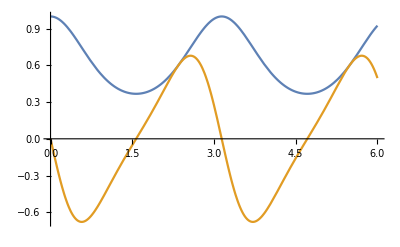

```mathematica
Plot[{f[x],f'[x]},{x,0,6}]
```

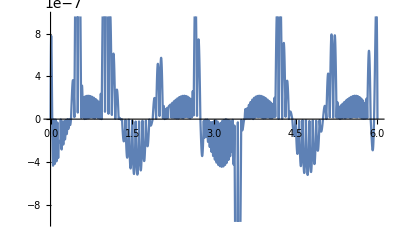

```mathematica
Plot[f[x]-Exp[-Sin[x]^2],{x,0,6}]
```

4. 点集的插值
ListInterpolation[array]
构建一个 InterpolatingFunction 对象，表示对给定数组进行插值的近似函数.

ListInterpolation[array, {{xmin, xmax}, {ymin, ymax}, …}]
指定 array 中的值来自的格点的域.可以用格线位置的确切列表代替 {xmin, xmax} 等.假设格线是等间距的.

ListInterpolation[array] 
假设格线在每个方向的整数位置.array 可以是任何维数的数组对应于有任何嵌套层数的列表.

ListInterpolation 支持 Method 选项.可能的设置包括样条插值的 "Spline" 和 Hermite 插值的 "Hermite".

```mathematica
f=ListInterpolation[{3,5,6,2,1,5}]
```

InterpolatingFunction[…]

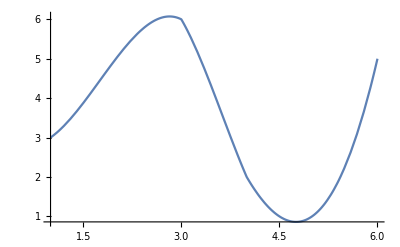

```mathematica
Plot[f[x],{x,1,6}]
```

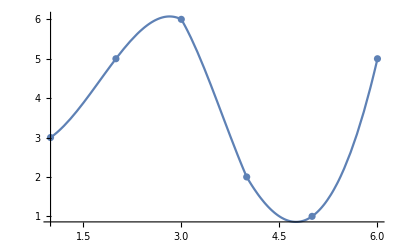

```mathematica
Show[%,ListPlot[{3,5,6,2,1,5}]]
```

```mathematica
g=ListInterpolation[{3,5,6,2,1,5},{{0,1}}]
```

InterpolatingFunction[…]

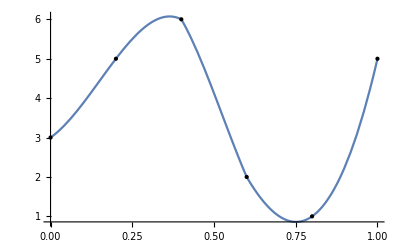

```mathematica
Plot[g[x],{x,0,1},Epilog->MapIndexed[Point[{(#2[[1]]-1)/5,#1}]&,{3,5,6,2,1,5}]]
```

```mathematica
Clear[f,x,y];
```

```mathematica
f=ListInterpolation[Table[Sin[x y],{x,0,1,.25},{y,0,2,.25}],{{0,1},{0,2}}]
Show[{Plot3D[f[x,y],{x,0,1},{y,0,2}],Graphics3D[{Red,PointSize[0.03],Table[Point[{x,y,Sin[x y]}],{x,0,1,.25},{y,0,2,.25}]}]}]
```

InterpolatingFunction[…]

-Graphics3D-

## 6.2 曲线拟合

曲线拟合即是利用最小二乘原理将型值进行分析运算，以求出最接近或最能表示数据趋势的函数。多项式插值要求多项式曲线必须穿过所在区间上的每个数据点。如果在全区间[x0, xn] 找插值函数，当n较大时常会引起插值曲线, 在区间端点附近的剧烈振荡 （称为 Runge 现象）。从实验者的角度看，要求逼近曲线 C, 穿过每个数据点，既无这种必要，又无进一步提高逼近精度的可能，因为数据点本身就带有各种误差。构造一条次数较低 （记为 s) 的多项式曲线 C, 只要求 C, 尽可能地贴近全部数据点，而不必穿过每一点。"尽可能地贴近"，通常选用最小二乘意义下的逼近，这就是一元拟合的概念。

```mathematica
1.线性拟合
```

Fit[data, {f1, …, fn}, {x, y, …}]
求变量 {x, y, …} 的函数 f1, …, fn 的 data 列表拟合 a1 f1 + … + an fn.

data 可以是以下格式：{v1, …, vn} 等同于 {{1, v1}, …, {n, vn}}
{{x1, v1}, …, {xn, vn}} 在坐标 xi 具有值 vi 的单变量数据
{{x1, y1, v1}, …} 在坐标 {xi, yi} 具有值 vi 的双变量数据
{{x1, y1, …, v1}, …} 在坐标 {xi, yi, …} 具有值 vi 的多变量数据

例题 : 设某次实验数据如下 :
 x 1.36 1.45 1.58 1.69 1.92 2.13
y 14.12 15.09 16.82 17.56 18.43 19.75
分别用一次多项式和二次多项式拟合.

```mathematica
data={{1.36,14.12},{1.45,15.09},{1.58,16.82},{1.69,17.56},{1.92,18.43},{2.13,19.75}};
```

```mathematica
f1=Fit[data,{1,x},x]
```

5.17696+6.98008 x

```mathematica
f2=Fit[data,{1,x,x^2},x]
```

-13.7595+29.2217 x-6.37205 x^2

```mathematica
f4=Fit[data,{1,x,x^2,x^3,x^4},x]
```

456.21-1131.44 x+1057.25 x^2-428.477 x^3+64.0084 x^4

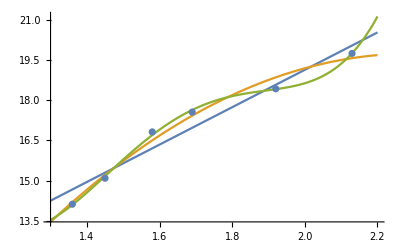

```mathematica
Show[Plot[{f1,f2,f4},{x,1.3,2.2}],ListPlot[data]]
```

例题 : 已知点列 {{0, 0}, {0.4, 0.1010}, {0.8, 0.8516}, {1.2, 1.0476}, {1.6, 3.0750}, {2.0, 3.4993}, {2.4, 6.0650}, {2.8, 7.9027}, {3.2, 9.7048}, {3.6, 13.9593}, {4.0, 14.6776}}, 
用多项式和三角函数 {1, x, x^2, x^3, Sin[x], Sin[2 x], Sin[3 x]} 做线性拟合。

```mathematica
data={{0,0},{0.4,0.1010},{0.8,0.8516},{1.2,1.0476},{1.6,3.0750},{2.0,3.4993},{2.4,6.0650},{2.8,7.9027},{3.2,9.7048},{3.6,13.9593},{4.0,14.6776}};
```

```mathematica
g=Fit[data,{1,x,x^2,x^3,Sin[x],Sin[2x],Sin[3x]},x]
```

-0.0225284+12.2698 x-4.16065 x^2+0.410269 x^3-8.42084 Sin[x]-0.456135 Sin[2 x]-0.441011 Sin[3 x]

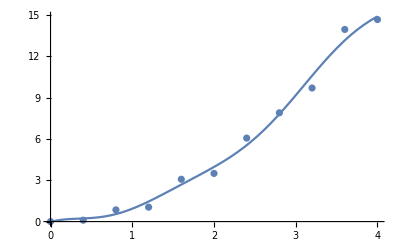

```mathematica
Show[Plot[g,{x,0,4}],ListPlot[data]]
```

例题：已知数据点集
{x, y, z} = {{0, 0, 0.03}, {0, 1, 0.15}, {0, 2, 0.67}, {0, 3, 1.82}, {0, 4, 1.53}, {1, 0, 0.55}, {1, 1, 0.93}, {1, 2, 3.42}, {1, 3, 5.07}, {1, 4, 2.66}, {2, 0, 2.35}, {2, 1, 0.47}, {2, 2, 2.88}, {2, 3, 0.49}, {2, 4, 0.33}, {3, 0, 2.11}, {3, 1, 0.86}, {3, 2, 3.14}, {3, 3, 1.59}, {3, 4, 0.62}}
试求矩形域 D = [0, 3] X[0, 4] 上的二元拟合多项式P1 (x, y), P2 (x, y)，P3 (x, y).

```mathematica
data={{0,0,0.03},{0,1,0.15},{0,2,0.67},{0,3,1.82},{0,4,1.53},{1,0,0.55},{1,1,0.93},{1,2,3.42},{1,3,5.07},{1,4,2.66},{2,0,2.35},{2,1,0.47},{2,2,2.88},{2,3,0.49},{2,4,0.33},{3,0,2.11},{3,1,0.86},{3,2,3.14},{3,3,1.59},{3,4,0.62}};
```

```mathematica
p1=Fit[data,{1,x,y},{x,y}]
p2=Fit[data,{1,x,y,x y,x^2,y^2},{x,y}]
p3=Fit[data,{1,x,y,x y,x^2,y^2,x^3,x^2 y,x y^2,y^3},{x,y}]
```

1.058+0.125 x+0.169 y

-0.669129+1.7823 x-0.3315 x^2+1.46896 y-0.3314 x y-0.200714 y^2

-0.382557+4.95175 x-3.603 x^2+0.748333 x^3-1.09094 y-0.0679714 x y-0.048 x^2 y+1.47157 y^2-0.0298571 x y^2-0.27125 y^3

```mathematica
Show[Plot3D[p1,{x,0,3},{y,0,4}],ListPointPlot3D[data]]
Show[Plot3D[p2,{x,0,3},{y,0,4}],ListPointPlot3D[data]]
Show[Plot3D[p3,{x,0,3},{y,0,4}],ListPointPlot3D[data]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

### 2. 最佳拟合

FindFit[data, expr, pars, vars]
求出参数 pars 的数值，使 expr 作为关于 vars 的函数给出对 data 最佳拟合

FindFit[data, {expr, cons}, pars, vars]
在带参量的约束条件 cons 下，求最佳拟合.

data 可以采用形式 {{x1, y1, …, f1}, {x2, y2, …, f2}, …}，其中坐标 x, y, … 的个数等于列表 vars 中变量的个数.data 也可以采用形式 {f1, f2, …}，假定单坐标取值 1、2、….在线性情况下，

FindFit 求出全局最优拟合.在非线性情况下，FindFit 通常求出局部最优拟合.

```mathematica
data={15.2,20.6,27.3,36.7,49.2,65.6,87.6};
model=a Exp[b x];
f=FindFit[data,model,{a,b},x]
```

{a→11.4776,b→0.290456}

## 6.3 数值积分

NIntegrate[f(x),{x,xmin,xmax}] 一元函数数值积分

NIntegrate[f(x,y,…),{x,xmin,xmax},{y,ymin,ymax}] 多元函数数值积分

NIntegrate[f(x,y,…),{x,y,…}∈reg] 在区域reg上数值积分

NIntegrate[f[x],{x,xmin,x1,x2,…,xmax}]沿直线段求数值积分，从点 xmin 开始,经过点x1,x2,…,到 xmax.

```mathematica
Integrate[Sin[Sin[x]],{x,0,1}]
NIntegrate[Sin[Sin[x]],{x,0,1}]
```

0

0.430606

求数值积分时，Mathematica 并不直接察看被积函数的函数形式.它简单地求一系列被积函数在特定点的近似函数值，然后取这些值从中导出积分的近似值.应注意的一个要点是 Mathematica 求数值积分时，它具有的被积函数的信息仅仅是被积函数的一系列数值值.要得到积分的确切结果，Mathematica 必须对被积函数的光滑性和其它性质做出某种假定.如果被积函数是严重病态的，这些假定可能失效，因此, Mathematica 可能给出错误结果.

```mathematica
NIntegrate[Exp[-x^2],{x,-10,10}]
NIntegrate[Exp[-x^2],{x,-10000,10000}]
```

1.77245

0.

例题：多元函数积分

（1） 计算平面图形面积.

```mathematica
NIntegrate[Boole[1/4≤x^2+(2 y)^2≤1∧y>x],{x,-1,1},{y,-1,1}]
```

0.589049

(2) 随机区域上的三重积分

```mathematica
A=ConvexHullMesh[RandomReal[10,{50,3}]]
```

-Graphics3D-

```mathematica
NIntegrate[x^2 y^2 z^2,{x,y,z}∈A]
```

1.2129×10^7

指定运算结果的精度 :

如果使用 Integrate, 然后使用 N得到 数值结果，那么 N 的第二个自变量指定了精度.

对于 NIntegrate指令 可以使用选项 WorkingPrecision -> n 指定精度.

```mathematica
NIntegrate[1/x,{x,1,2},WorkingPrecision->40]
NIntegrate[1/(1+Sqrt[x]),{x,0,1},PrecisionGoal->100,WorkingPrecision->200]
```

0.6931471805599453094172321214581765680755

0.6137056388801093811655357570836468638489997312794894917586399810132127560606105687882733460071626249159970379588586285326289595284837388859346584967298480761385498838450271890664634918876355517462432

其次，对于有奇点的积分，可以用Exclusions 排除.

例题：广义积分计算

```mathematica
NIntegrate[Log[x],{x,0,1}]
```

-1.

```mathematica
NIntegrate[1/(Sqrt[1-x] x^(1/5)),{x,0,1}]
```

2.29929

```mathematica
NIntegrate[{1/Sqrt[x+y],Log[x y]},{x,0,1},{y,0,1}]
```

{1.10457,-2.}

```mathematica
NIntegrate[Log[2-Sin[x]-Sin[y]],{x,0,4},{y,0,4},Exclusions->{{π/2,π/2}}]
```

-2.41908

积分区域排除使得被积函数的分母为零的曲线：

```mathematica
NIntegrate[1/Cos[x y],{x,0,5},{y,0,5},Exclusions->Cos[x y]==0]
```

3.84761

```mathematica
NIntegrate[1/(x-x^2),{x,-1,2},Method->"PrincipalValue",Exclusions->x-x^2==0]
```

1.38629

## 6.4 微分方程数值解

NDSolve 函数求常微分方程数值解。

近似数值求解的最大优点是不受方程类型的限制，即可以求任何形状微分方程的解 （当然要假定解的存在），但是求出的解只能是数值的 (即数据形式的) 解函数

NDSolve[eqns，y，{x，xmin, xmax}]
对常微分方程或方程组 eqns，求函数 y 关于x在[xmin, xmax] 范围内的数值解

NDSolve[{eqnl, eqn2, ...}, {yl, y2, ...}, {x, xmin, xmax}]
对常微分方程组，求函数 yl，y2, …关于；x 在[xmin, xmax] 范围内的数值解。

NDSolve 将函数 y 的解表示为 InterpolatingFunction 对象.这种对象提供独立变量x 从xmin 到xmax上的 M 的近似值.
 NDSolve 用迭代法求解.要进行计算，必须给定y[x] 和其导数y'[x] 的适当的初始或边界条件.给定的初始或边界条件必须能完全确定的解.一个典型的情形是n 阶微分方程需要给出直到n - 1 阶导数的初始条件，或给出在n个点处的边界条件.

```mathematica
NDSolve[{y'[x]==y[x],y[0]==1},y,{x,0,2}]
```

{{y→InterpolatingFunction[…]}}

```mathematica
NDSolve[{y'[x]+x y[x]==0,y[0]==1,y[1]==1},y,{x,0,1}]
```

NDSolve[{x y[x]+y'[x]==0,y[0]==1,y[1]==1},y,{x,0,1}]

{{y→InterpolatingFunction[…]}}

InterpolatingFunction[…]

4.95303

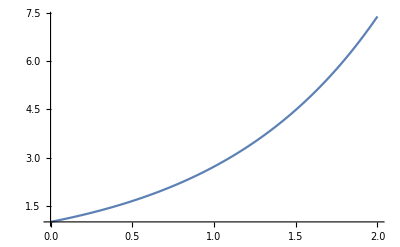

```mathematica
S1=NDSolve[{y'[x]==y[x],y[0]==1},y,{x,0,2}]
f=S1[[1,1,2]]
f[1.6]
Plot[f[x],{x,0,2}]
```

例题：求 y''' + y'' sin y = Sqrt[y], 在[0，10] 上满足条件 y (0) = 0, y' (0) = 0.5, y'' (0) = 1 的数值解。

```mathematica
S2=NDSolve[{y'''[x]+y''[x] Sin[y[x]]==Sqrt[y[x]],y[0]==0,y'[0]==0.5,y''[0]==1},y,{x,0,10.0}]
```

{{y→InterpolatingFunction[…]}}

例题：求解微分方程组     
x' (t) = -y (t) - x (t)^2
y' (t) = 2 x (t) - y (t)          t ∈ [0, 10] 
x (0) = y (0) = 1,

```mathematica
S3=NDSolve[{x'[t]==-y[t]-x[t]^2,y'[t]==2 x[t]-y[t],x[0]==1,y[0]==1},{x,y},{t,0,10}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

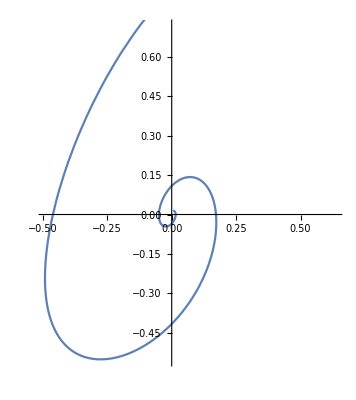

```mathematica
x=S3[[1,1,2]];
y=S3[[1,2,2]];
ParametricPlot[{x[t],y[t]},{t,0,10}]
```

例题：求解微分方程组
y1' (x) = -5 y1 (x)
y2' (x) = y1 (x) - y2 (x)
y3' (x) = y2 (x) - y3 (x)
y4' (x) = y3 (x) - y4 (x)
y5' (x) = 2 y4 (x)
y1 (0) = 1, y2 (0) = y3 (0) = y4 (0) = y5 (0) = 0

{y[2]'[x]==y[1][x]-y[2][x],y[3]'[x]==y[2][x]-y[3][x],y[4]'[x]==y[3][x]-y[4][x],y[1]'[x]==-5 y[1][x],y[5]'[x]==2 y[4][x],y[1][0]==1,y[2][0]==0,y[3][0]==0,y[4][0]==0,y[5][0]==0}

{{y[1]→InterpolatingFunction[…],y[2]→InterpolatingFunction[…],y[3]→InterpolatingFunction[…],y[4]→InterpolatingFunction[…],y[5]→InterpolatingFunction[…]}}

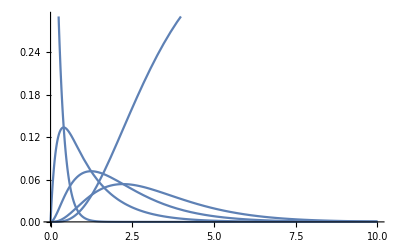

```mathematica
eqns=Join[Table[y[i]'[x]==y[i-1][x]-y[i][x],{i,2,4}],{y[1]'[x]==-5y[1][x],y[5]'[x]==2y[4][x],y[1][0]==1},Table[y[i][0]==0,{i,2,5}]]
 S4=NDSolve[eqns,Table[y[i],{i,5}],{x,0,10}]
 For[i=1,i≤5,i++,y[i]=S4[[1,i,2]]]
 Plot[Table[y[i][x],{i,1,5}],{x,0,10}]
```

NDSolve 允许用户指定结果的精度或准确度.一般，NDSolve 使步长越来越小，直到得出满足 AccuracyGoal 或 PrecisionGoal 的解为止.NDSolve 使用由用户给定的 WorkingPrecision 来决定内部计算中使用的总位数.给出的 WorkingPrecision 的值应该比 AccuracyGoal 或 PrecisionGoal 的值大.缺省设置 Automatic 下，AccuracyGoal PrecisionGoal 都等于 WorkingPrecision 减去 10 位.

### 2. 偏微分方程

NDSolve[eqns, y, {x, xmin, xmax}, {t, tmin, tmax}] 求偏微分方程数值解

NDSolve[eqns, u, {t, tmin, tmax}, {x, y} ∈ Ω] 在区域 Ω 上求解时间相关偏微分方程 eqns.

例题 求弦振动方程 u_tt = 4 u_xx 满足下面定解条件的特解。
        边界条件 u (0, t) = u (π, t) = 0 
        初始条件 u (x, 0) = sin⁡x u_t (x, 0) = 0

```mathematica
NDSolve[{D[u[x,t],{t,2}]==4 D[u[x,t],{x,2}],u[0,t]==0,u[Pi,t]==0,u[x,0]==Sin[x],Derivative[0,1][u][x,0]==0},u,{x,0,Pi},{t,0,60}]
 Plot3D[Evaluate[u[x,t]/.%],{x,0,Pi},{t,0,60},PlotRange->All]
```

{{u→InterpolatingFunction[…]}}

-Graphics3D-

例题 求解一维热传导方程 u_t = u_xx, u (t, 0) = sin⁡t, u (t, 5) = 0, u (0, x) = 0

```mathematica
NDSolve[{D[u[t,x],t]==D[u[t,x],x,x],u[0,x]==0,u[t,0]==Sin[t],u[t,5]==0},u,{t,0,10},{x,0,5}]
```

{{u→InterpolatingFunction[…]}}

```mathematica
Plot3D[Evaluate[u[t,x]/.%],{t,0,10},{x,0,5},PlotRange->All]
```

-Graphics3D-

## 6.5 规划问题

数学规划又称为优化方法，是运筹学的一个重要分支，在科学技术和工程实际中有着广泛的应用。一般将数学规划分为线性规划与非线性规划两大类型。假设一个函数 f有n个变量，现在要求f的最小值，但必须满足一个或多个约束条件，如果函数f和这些约束条件都是线性的就称线性规划，否则称其为非线性规划。

线性规划问题就是求一个线性函数在线性约束条件下的最值问题，通常形如:线性约束条件
a_11 x_1+a_12 x_2+⋯+a_(1n)x_n≥b_1
a_21 x_1+a_22 x_2+⋯+a_(2n)x_n≥b_2
......
a_m1 x_1+a_m2 x_2+⋯+a_mn x_n≥b_m
x_1≥0,x_2≥0,(…x)_n≥0
 求 min(c_1 x_1+c_2 x_2+⋯+c_n x_n).
此问题可以规范化写为：
X=(x_1,x_2,…,x_n),c=(c_1,c_2,…,c_n),b=(b_1,b_2,…,b_m), 
A=(a_11 | a_12 | ... | a_(1n)
a_21 | a_22 | ... | a_(2n)
... | ... | ... | ...
a_m1 | a_m2 | ... | a_mn),l=(l_1,l_2,…,l_n)

满足约束条件 AX≥b(≤或=)，X_i≥l_i 的向量 X 称为一个可行点，可行点全体所组成的集合s 称为可行域,求解线性规划的最终目的就是要在可行域 S 上寻求到一点  X^*,使目标函数值f(X^*)=(c∙X)^*在S 上达到极小

LinearProgramming[c, A, b] 求向量 X，使 c.X 在约束条件 AX >= b 和 X >= 0 下达到极小.

LinearProgramming[c, A, {{b1, s1}, {b2, s2}, …}] 求向量 X，使 c.X 在 X >= 0 和由矩阵 A 和 {bi, si} 确定的约束下达到最小.对于 A 的每个行 Ai，如果 si == 1，则相应的约束是 Ai.x >= bi，如果 si == 0，则为 Ai.x == bi，如果 si == -1，为 Ai.x <= bi.

LinearProgramming[c, A, b, {l1, l2, …}] 在由 A、b 和 xi >= li 确定的约束下最小化 c.X.

LinearProgramming[c, A, b, {{l1, u1}, {l2, u2}, …}] 在由 A、b 和 li <= xi <= ui 确定的约束下最小化 c.x.

LinearProgramming[c, A, b, lu, dom] 取在域 dom 内的 X 的元素，它是 Reals 或 Integers.

例题：在约束条件 {x + 2 y >= 2,   2 x - 3 y >= -6,   x >= 0, y >= 0} 下 求 min (2 x + 3 y) .

```mathematica
LinearProgramming[{2,3},{{1,2},{2,-3}},{2,-6}]
```

{0,1}

例题：在约束 {2 x_ 1 + 4 x_ 2 + 5 x_ 3 <= 100, x_ 1 + 2 x_ 2 + 3 x_ 3 >= 6,  x_ 1 >= -1, x_ 2 >= -1, 3 >= x_ 3 >= -1} 条件下计算   
max (4 x_ 1 + 5 x_ 2 + 3 x_ 3).

```mathematica
c={4,5,3} ;A={{2,4,5},{1,2,3}}
```

{{2,4,5},{1,2,3}}

```mathematica
LinearProgramming[-c,A,{{100,-1},{6,1}},{{-1,Infinity},{-1,Infinity},{-1,3}}]
```

{109/2,-1,-1}

求最大值，参数取 - c，约束条件中有 >=, <= , 可以通过加 "-"改变不等式方向，也可以在bi后跟 1，-1，0 来说明不等式方向.

例题：一汽车厂生产大中小三种型号的汽车，每种汽车需要钢材和加工时间，利润以及工厂现有每月总量如下表所示，试制定生产规划，使利润最大.
□ | 小型 | 中型 | 大型 | 拥有量
钢材 (吨) | 1.5 | 3 | 5 | 700
工时 （时） | 280 | 250 | 400 | 80000
利润 （万元） | 2 | 3 | 4 | □

求 max (2 x_1 + 3 x_2 + 4 x_3) 
满足：{1.5 x_1 + 3x_2 + 5 x_3 <= 700，280x_1+ 250 x_2 + 400x_3 <= 80000，
x_1, x_2, x_3 为非负整数

```mathematica
c={2,3,4};
A={{1.5,3,5},{280,250,400}};
b={700,80000};
x=LinearProgramming[-c,-A,-b,0,Integers]
 c.x
```

{140,163,0}

769

LinearOptimization[f, cons, vars] 求能最小化受线性约束条件 cons 限制的线性目标函数 f 的变量 vars 的值.

LinearOptimization[c, {a, b}] 求能最小化受线性不等式约束条件ax + b >= 0 限制的线性目标函数 c.x 的实向量 x.

LinearOptimization[c, {a, b}, {aeq, beq}] 求能最小化受包括ax + b >= 0 以及线性等式约束条件a_eq x + b_eq = 0 限制的线性目标函数 c.x 的实向量 x.

例题：在约束条件 {x + 2 y >= 2， 2 x - 3 y >= -6， x >= 0, y >= 0} 下 求 min⁡ (2 x + 3 y)

```mathematica
Clear["Global`*"]
LinearOptimization[2x+3y,{x+2y≥2,2x-3y≥-6,x≥0,y≥0},{x,y}] 
LinearOptimization[{2,3},{{{1,2},{2,-3},{1,0},{0,1}},{-2,6,0,0}}]
```

{x→0,y→1}

{0,1}

例题：最小化受约束条件 x + 2 y == 3, x >= 0.5, y >= 0 限制的 x + y

```mathematica
LinearOptimization[x + y, {x + 2 y == 3, x >= 0.5, y >= 0}, {x, y}]
```

{x→0.5,y→1.25}

```mathematica
LinearOptimization[{1, 1}, {{{1, 0}, {0, 1}}, {-0.5, 0}}, {{{1, 2}}, {-3}}]
```

{0.5,1.25}

### 非线性规划

在 Mathematica 中可利用 FindMinimum 函数进行非线性规划求极小值

FindMinimum[{f[x, y], 约束条件}，{x, y}]

FindMinimum[f[x], x] 用最速下降路径求f (x) 的极小值。

FindMinimum[f[x, y], {{x, x0}, {y, y0}}] 在 （x0, y0） 附近的极小值。

例题 求函数 f (x) = xsinx 在约束条件 1 <= x <= 15 下的极小值。

```mathematica
FindMinimum[{x Sin[x],1≤x≤15},x]
```

{-4.81447,{x→4.91318}}

例题 求函数 x + y 在约束条件 x Cos x + 2 y >= 3, x >= 0, y >= 0 在 x = 3, y = 4 附近的极小值.

```mathematica
FindMinimum[{x+y,x Cos[x]+2y≥3&&x≥0&&y≥0},{x,3},{y,4}]
```

{1.5,{x→1.71822×10^-7,y→1.5}}